# Liquid Crystal Laplacian By Jackson Burzynski, Raewyn Duvall, and Ben Nissan In this notebook we solve for the liquid crystal configuration in contact with a patterned surface. Effectively, solving this problem involves solving Laplace’s equation ∇^2 θ = 0 with the proper boundary conditions. To solve the Laplace equation, two different methods are used: Finite Difference and Finite Elements. We implement both algorithms and compare the energy in the LC configuration between both solutions and an analytical solution to the problem.

## Part I: Simplifying the Free Energy Expression We start by simplifying the free energy expression to prove that the minimizer is given by ∇^2 θ = 0

```mathematica
ClearAll[x,y,z,θ,ϕ]
```

First we define the director

```mathematica
n={Cos[θ[x,y]]Cos[ϕ],Cos[θ[x,y]]Sin[ϕ],Sin[θ[x,y]]};
```

```mathematica
(Div[n,{x,y,z}])^2+(n.Curl[n,{x,y,z}])^2+Cross[n,Curl[n,{x,y,z}]].Cross[n,Curl[n,{x,y,z}]]//Simplify
```

(θ^(0,1)[x,y])^2+(θ^(1,0)[x,y])^2

```mathematica
Grad[θ[x,y],{x,y,z}].Grad[θ[x,y],{x,y,z}]
```

(θ^(0,1)[x,y])^2+(θ^(1,0)[x,y])^2

Thus we have reduced the complicated free energy expression to (∇θ)^2

## Part II: The Finite Difference Approach Next we apply the method of Finite Differences to solve the Laplace Equation.

#### Define the Matrices

```mathematica
(* Function to construct the matrix and right hand side of our matrix equation *)
finiteDifferenceMatrices[nn_,xdim_,zdim_]:=Block[{M,P,Matrix,θ0},
(* Build the main Matrix *)
M=SparseArray[Join[
Table[{i,i}->1,{i,1,xdim}],(* boundary conditions *)
Table[{i,i}->1,{i,nn-xdim+1,nn}],
Table[{i,i}->-4,{i,xdim,nn-xdim}],(* diagonal *)
Table[{i,i+1}->1,{i,xdim+1,nn-xdim}],(* right neighbors *)
Table[{i,i-1}->1,{i,xdim+1,nn-xdim}],(* left neighbors *)
Table[{i,i-xdim}->1,{i,xdim+1,nn-xdim}], (* bottom neighbors *) 
Table[{i,i+xdim}->1,{i,xdim+1,nn-xdim}], (* top neighbors *)
Table[{i,i-1}->0,{i,xdim+1,nn-xdim,xdim}]
],{nn,nn}];
(* Build the matrix to handle periodic boundary conditions *)
P = SparseArray[Join[
Table[{i,i+xdim-1}->1,{i,xdim+1,nn-xdim,xdim}], (* left neighbor *)
Table[{i,i-1}->-1,{i,xdim+1,nn-xdim,xdim}],(* remove previous left neighbor *)
Table[{i,i-xdim+1}->1,{i,2*xdim,nn-xdim,xdim}],(* right neighbor *)
Table[{i,i+1}->-1,{i,2*xdim,nn-xdim,xdim}] (* remove previous right neighbor *)
],{nn,nn}];
(* Sum the matrices to obtain the correct matrix *)
Matrix = M+P;
(* Build the right hand side *)
θ0 = SparseArray[Join[
Table[{i,1}->Pi/2,{i,1,xdim/2}],
Table[{i,1}->Pi/2,{i,nn-xdim+1,nn-xdim/2}]
],{nn,1}];
Return[{Matrix,θ0}];]
```

```mathematica
(* Define the dimensions of our run *)
xdim = 10;
zdim = 10;
dims = xdim*zdim;
```

```mathematica
(* get the matrices *)
```

```mathematica
x=finiteDifferenceMatrices[dims,xdim,zdim]//N;
sol=Flatten[LinearSolve[x[[1]],x[[2]]]];
matrix = Partition[sol,xdim];
```

```mathematica
ListPlot3D[matrix]
```

-Graphics3D-

#### Calculate the Energy

We must calculate the integral F=1/2∫(∇θ)^2dV

```mathematica
calcEnergy[sol_,grid_]:=Block[{theta,interp,der,energy},
theta =Map[Flatten,Transpose[{grid,Flatten[sol]}],1];
interp=Interpolation[theta];
der={Derivative[1,0][interp],Derivative[0,1][interp]};
energy = NIntegrate[der[[1]][x,z]der[[1]][x,z]+der[[2]][x,z]der[[2]][x,z],{x,0,1},{z,0,1}];
Return[energy];
]
```

```mathematica
grid[xdim_,zdim_] := Table[{N[x],N[z]},{z,0,1,1/(zdim)},{x,0,1,1/( xdim)}];
x=Flatten[grid[xdim-1,zdim-1],1];
```

```mathematica
calcEnergy[matrix,x]
```

6.57545

```mathematica
(* TODO: make a plot of energy vs discretization size *)
```

## Part III: The Finite Element Approach We now solve the same problem by using the method of Finite Elements

### The Mesh We begin by defining our computational mesh

```mathematica
grid[xdim_,zdim_] := Table[{N[x],N[z]},{z,0,1,1/(zdim)},{x,0,1,1/( xdim)}];
```

```mathematica
x=Flatten[grid[xdim,zdim],1];
```

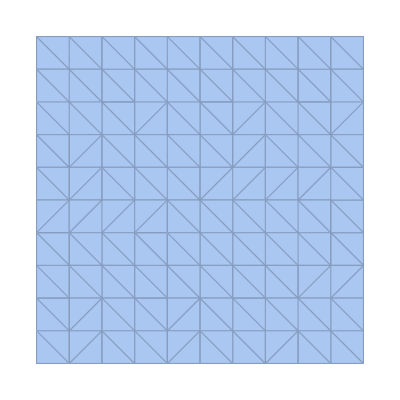

```mathematica
mesh = DelaunayMesh[x]
```

### Basis Functions We must define our basis functions v_n(x,z) to be 1 on the n^th grid point and 0 elsewhere

```mathematica
base[i_,j_,xdim_,zdim_] := Map[Flatten,Transpose[{Flatten[grid[xdim,zdim],1],Flatten[Table[If[{i,j}=={k,m},1,0],{k,xdim+1},{m,zdim+1}]]}]];
```

```mathematica
Manipulate[ListPlot3D[base[i,j,xdim,xdim]],{i,1,xdim+1,1},{j,1,xdim+1,1}]
```

```mathematica
ListPlot3D[base[5,4,xdim,zdim]]
```

-Graphics3D-

### The Inner Products We must define two matrices of inner products in order to calculate for the LC configuration L_ij=⟨∇v_i,∇v_j⟩=∫∇v_i∇v_jdx and M_ij=⟨v_i,v_j⟩=∫v_i v_j dx Thus, we must determine the overlap between adjacent basis functions and their derivatives

```mathematica
vtest=Flatten[Table[Interpolation[base[i,k,xdim,zdim],InterpolationOrder->1],{k,xdim},{i,xdim}],1];
```

```mathematica
xtest=grid[xdim,zdim];
```

#### L_ij=⟨∇v_i,∇v_j⟩

First we compute the diagonal elements by taking ⟨∇v_i,∇v_i⟩

```mathematica
testpos = 46;
```

```mathematica
fun = vtest[[testpos]];
```

```mathematica
grad={Derivative[1,0][fun],Derivative[0,1][fun]};
```

```mathematica
Plot3D[grad[[1]][x,z]grad[[1]][x,z]+grad[[2]][x,z]grad[[2]][x,z],{x,0,1},{z,0,1}]
```

-Graphics3D-

```mathematica
Lii=NIntegrate[grad[[1]][x,z]grad[[1]][x,z]+grad[[2]][x,z]grad[[2]][x,z],{x,0,1},{z,0,1}]
```

2.66667

Next we compute the off diagonal elements. We will have 8 off diagonals, one from each neighboring
basis function. We start with the left/right/top/bottom neighbors

```mathematica
fun2 = vtest[[testpos+1]];
```

```mathematica
grad2={Derivative[1,0][fun2],Derivative[0,1][fun2]};
```

```mathematica
Plot3D[grad[[1]][x,z]grad2[[1]][x,z]+grad[[2]][x,z]grad2[[2]][x,z],{x,0,1},{z,0,1}]
```

-Graphics3D-

```mathematica
Lij=NIntegrate[grad[[1]][x,z]grad2[[1]][x,z]+grad[[2]][x,z]grad2[[2]][x,z],{x,0,1},{z,0,1}]
```

-0.333333

Now we calculate the overlap from the diagonal neighbors

```mathematica
fun3 = vtest[[testpos+xdim-1]];
```

```mathematica
grad3={Derivative[1,0][fun3],Derivative[0,1][fun3]};
```

```mathematica
Plot3D[grad[[1]][x,z]grad3[[1]][x,z]+grad[[2]][x,z]grad3[[2]][x,z],{x,0,1},{z,0,1}]
```

-Graphics3D-

```mathematica
LijDiag=NIntegrate[grad[[1]][x,z]grad3[[1]][x,z]+grad[[2]][x,z]grad3[[2]][x,z],{x,0,1},{z,0,1}]
```

-0.333333

#### M_ij=⟨v_i,v_j⟩

⟨v_i,v_j⟩

First we calculate the diagonal elements of the matrix M

```mathematica
(* Diagonal Elements *)
```

```mathematica
Plot3D[vtest⟦testpos⟧[x,z]vtest⟦testpos⟧[x,z],{x,0,1},{z,0,1},PlotRange-> All]
```

-Graphics3D-

```mathematica
Mii=NIntegrate[vtest⟦testpos⟧[x,z]vtest⟦testpos⟧[x,z],{x,0,1},{z,0,1}]
```

0.00444444

Next we calculate the overlap from the 8 neighboring basis functions. We start by calculating the left/right/top/bottom
neighbors

```mathematica
Plot3D[vtest⟦testpos⟧[x,z]vtest⟦testpos+1⟧[x,z],{x,0,1},{z,0,1},PlotRange-> All]
```

-Graphics3D-

```mathematica
Mij = NIntegrate[vtest⟦testpos⟧[x,z]vtest⟦testpos+1⟧[x,z],{x,0,1},{z,0,1}]
```

0.00111111

Next we calculate the overlap from the diagonal neighbors

```mathematica
Plot3D[vtest⟦testpos⟧[x,z]vtest⟦testpos+xdim-1⟧[x,z],{x,0,1},{z,0,1},PlotRange-> All]
```

-Graphics3D-

```mathematica
MijDiag=NIntegrate[vtest⟦testpos⟧[x,z]vtest⟦testpos+xdim-1⟧[x,z],{x,0,1},{z,0,1}]
```

0.000277778

#### Buildiing the Matrices

```mathematica
(* Function to construct the matrix and right hand side of our matrix equation *)
finiteElementMatrices[nn_,xdim_,zdim_]:=Block[{L,M,LL,LP,MP,MM,b},
(* Build the left Matrix *)
L=SparseArray[Join[
Table[{i,i}->1,{i,1,xdim}],(* boundary conditions *)
Table[{i,i}->1,{i,nn-xdim+1,nn}],
Table[{i,i}->Lii,{i,xdim,nn-xdim}],(* diagonal *)
Table[{i,i+1}->Lij,{i,xdim+1,nn-xdim}],(* right neighbors *)
Table[{i,i-1}->Lij,{i,xdim+1,nn-xdim}],(* left neighbors *)
Table[{i,i-xdim}->Lij,{i,xdim+1,nn-xdim}], (* bottom neighbors *) 
Table[{i,i+xdim}->Lij,{i,xdim+1,nn-xdim}], (* top neighbors *)
Table[{i,i+xdim-1}->LijDiag,{i,xdim+1,nn-xdim}],(* upper left *)
Table[{i,i+xdim+1}->LijDiag,{i,xdim+1,nn-xdim-1}], (* upper right *)
Table[{i,i-xdim-1}->LijDiag,{i,xdim+2,nn-xdim}], (* bottom left *)
Table[{i,i-xdim+1}->LijDiag,{i,xdim+1,nn-xdim}] (* bottom right *)
],{nn,nn}];
(* Build the right matrix *)
M=SparseArray[Join[
Table[{i,i}->1,{i,1,xdim}],(* boundary conditions *)
Table[{i,i}->1,{i,nn-xdim+1,nn}],
Table[{i,i}->Mii,{i,xdim,nn-xdim}],(* diagonal *)
Table[{i,i+1}->Mij,{i,xdim+1,nn-xdim}],(* right neighbors *)
Table[{i,i-1}->Mij,{i,xdim+1,nn-xdim}],(* left neighbors *)
Table[{i,i-xdim}->Mij,{i,xdim+1,nn-xdim}], (* bottom neighbors *) 
Table[{i,i+xdim}->Mij,{i,xdim+1,nn-xdim}], (* top neighbors *)
Table[{i,i+xdim-1}->MijDiag,{i,xdim+1,nn-xdim}],(* upper left *)
Table[{i,i+xdim+1}->MijDiag,{i,xdim+1,nn-xdim-1}], (* upper right *)
Table[{i,i-xdim-1}->MijDiag,{i,xdim+2,nn-xdim}], (* bottom left *)
Table[{i,i-xdim+1}->MijDiag,{i,xdim+1,nn-xdim}] (* bottom right *)
],{nn,nn}];
(* Build matrix to handle periodic boundary conditions *)
(* to implement, place negative elements in places where there
shoud not be matrix elements, and positive elements where there 
should be elements *)
LP = SparseArray[Join[
Table[{i,i+xdim-1}->(Lij-LijDiag),{i,xdim+1,nn-xdim,xdim}], (* replace left diag with left neighbor *)
Table[{i,i-1}->(-Lij+LijDiag),{i,xdim+1,nn-xdim,xdim}],(* remove previous left neighbor *)
Table[{i,i+2xdim-1}->LijDiag,{i,xdim+1,nn-xdim,xdim}], (* top left neighbor *)
Table[{i,i+xdim-1}->-LijDiag,{i,xdim+1,nn-xdim,xdim}],(* remove previous top left neighbor *)

Table[{i,i-xdim+1}->(Lij-LijDiag),{i,2*xdim,nn-xdim-1,xdim}],(* replace bottom right neighbor with right neighbor*)
Table[{i,i+1}->(-Lij+LijDiag),{i,2*xdim,nn-xdim,xdim}], (* replce previous right neighbor with top right*)
Table[{i,i+xdim+1}->-LijDiag,{i,2*xdim,nn-xdim-1,xdim}],(* remove previous top right neighbor *)
Table[{i,i-2*xdim-1}->LijDiag,{i,2*xdim,nn-xdim,xdim}] (* bottom right neighbor *)
],{nn,nn}];

MP = SparseArray[Join[
Table[{i,i+xdim-1}->(Mij-MijDiag),{i,xdim+1,nn-xdim,xdim}], (* replace left diag with left neighbor *)
Table[{i,i-1}->(-Mij+MijDiag),{i,xdim+1,nn-xdim,xdim}],(* remove previous left neighbor *)
Table[{i,i+2xdim-1}->MijDiag,{i,xdim+1,nn-xdim,xdim}], (* top left neighbor *)
Table[{i,i+xdim-1}->-MijDiag,{i,xdim+1,nn-xdim,xdim}],(* remove previous top left neighbor *)

Table[{i,i-xdim+1}->(Mij-MijDiag),{i,2*xdim,nn-xdim-1,xdim}],(* replace bottom right neighbor with right neighbor*)
Table[{i,i+1}->(-Mij+MijDiag),{i,2*xdim,nn-xdim,xdim}], (* replce previous right neighbor with top right*)
Table[{i,i+xdim+1}->-MijDiag,{i,2*xdim,nn-xdim-1,xdim}],(* remove previous top right neighbor *)
Table[{i,i-2*xdim+1}->MijDiag,{i,2*xdim,nn-xdim,xdim}] (* bottom right neighbor *)
],{nn,nn}];
MM = M+MP;
LL=L+LP;
(* Build the right hand side *)
b = SparseArray[Join[
Table[{i,1}->Pi/2,{i,1,xdim/2}],
Table[{i,1}->Pi/2,{i,nn-xdim+1,nn-xdim/2}]
],{nn,1}];
Return[{L,M,b}];]
```

#### Solving the System

```mathematica
solve[L_,M_,b_] := Block[{θ},
θ=LinearSolve[L,-M.b];
Return [θ];
]
```

```mathematica
xdim=25;
zdim=25;
dims = xdim*zdim;
```

```mathematica
mats = finiteElementMatrices[dims,xdim,zdim];
```

```mathematica
sol=Flatten[solve[mats[[1]],mats[[2]],mats[[3]]],1];
```

```mathematica
newmat =Partition[sol,xdim];
```

```mathematica
ListPlot3D[newmat]
```

-Graphics3D-

## Calculating the Energy

```mathematica
grid[xdim_,zdim_] := Table[{N[x],N[z]},{z,0,1,1/(zdim)},{x,0,1,1/( xdim)}];
x=Flatten[grid[xdim-1,zdim-1],1];
```

```mathematica
calcEnergy[newmat,x]
```

9.68472

## Part IV: Comparing Methods

## What Needs to be done Plot energy vs discretization size Determine how to use the Delaunay mesh Fix matrices to include proper boundary conditions Compare the results